```mathematica
Clear["Global`*"];
ssx1i={};
ssx1d={};
ssx2i={};
ssx2d={};
ssx3i={};
ssx3d={};
ssx4i={};
ssx4d={};
ssx5i={};
ssx5d={};
ssx6i={};
ssx6d={};
ssin={};
(* Initialize all the equations and parameters *)
sTot=4.048757;eTot=0.2562051;
dEs={D[x1[t],t]==-k1*x1[t]*x3[t]-k4*x1[t]*x4[t]+k2*x5[t]+k5*x6[t]+k7*x2[t],D[x2[t],t]==k3*x5[t]+k6*x6[t]-k7*x2[t],D[x3[t],t]==-k1*x1[t]*x3[t]+k2*x5[t]+k3*x5[t]-k8*x3[t]+k9*x4[t],D[x4[t],t]==-k4*x1[t]*x4[t]+k5*x6[t]+k6*x6[t]+k8*x3[t]-k9*x4[t],D[x5[t],t]==k1*x1[t]*x3[t]-k2*x5[t]-k3*x5[t]-k10*x5[t]+k11*x6[t],D[x6[t],t]==k4*x1[t]*x4[t]-k5*x6[t]-k6*x6[t]+k10*x5[t]-k11*x6[t]};
invaEs={x1[t]+x2[t]+x5[t]+x6[t]==sTot,x3[t]+x4[t]+x5[t]+x6[t]==eTot};
(*params = {k1->456.903,k2->0.2218406,k3->7.42964,k4->214.4758,k5->0.0012412,k6->1.249609,k7->0.3511192,k8->0.5229679,k9->20.04716,k10->0.2373376,k11->0.1077105};*)
(* Get the steady state first *)
tf=50000;
input=0.2;
icEs={x1[0]==sTot,x2[0]==0,x3[0]==input,x4[0]==0,x5[0]==0,x6[0]==0};
params = {k1->456.903,k2->0.2218406,k3->7.42964,k4->214.4758,k5->0.0012412,k6->1.249609,k7->0.3511192,k8->0.5229679,k9->20.04716,k10->0.2373376,k11->0.1077105};

sol=NDSolve[{dEs,icEs}/.params,{x1,x2,x3,x4,x5,x6},{t,0,tf}];

(*newIC={x1[0]==Evaluate[x1[tf]/.sol][[1]],x2[0]==Evaluate[x2[tf]/.sol][[1]],x3[0]==Evaluate[x3[tf]/.sol][[1]],x4[0]==Evaluate[x4[tf]/.sol][[1]],x5[0]==Evaluate[x5[tf]/.sol][[1]],x6[0]==Evaluate[x6[tf]/.sol][[1]]};*)

For[i=0,i≤1000,i++,
tf=50000;
(*newIC={x1[0]==Evaluate[x1[tf]/.sol][[1]],x2[0]==Evaluate[x2[tf]/.sol][[1]],x3[0]==Evaluate[x3[tf]/.sol][[1]]+0.001*i,x4[0]==Evaluate[x4[tf]/.sol][[1]],x5[0]==Evaluate[x5[tf]/.sol][[1]],x6[0]==Evaluate[x6[tf]/.sol][[1]]};*)
newIC={x1[0]==sTot,x2[0]==0,x3[0]==0.2+i*0.0001,x4[0]==0,x5[0]==0,x6[0]==0};
sol=NDSolve[{dEs,newIC}/.params,{x1,x2,x3,x4,x5,x6},{t,0,tf}];

ssx1i=Append[ssx1i,Evaluate[x1[tf]/.sol][[1]]]; 
ssx2i=Append[ssx2i,Evaluate[x2[tf]/.sol][[1]]];ssx3i=Append[ssx3i,Evaluate[x3[tf]/.sol][[1]]];ssx4i=Append[ssx4i,Evaluate[x4[tf]/.sol][[1]]];ssx5i=Append[ssx5i,Evaluate[x5[tf]/.sol][[1]]];ssx6i=Append[ssx6i,Evaluate[x6[tf]/.sol][[1]]]
];

For[i=0,i≤1000,i++,
tf=50000;
(*newIC={x1[0]==Evaluate[x1[tf]/.sol][[1]],x2[0]==Evaluate[x2[tf]/.sol][[1]],x3[0]==Evaluate[x3[tf]/.sol][[1]]-i*0.001,x4[0]==Evaluate[x4[tf]/.sol][[1]],x5[0]==Evaluate[x5[tf]/.sol][[1]],x6[0]==Evaluate[x6[tf]/.sol][[1]]};*)
newIC={x1[0]==sTot,x2[0]==0,x3[0]==0.3-i*0.0001,x4[0]==0,x5[0]==0,x6[0]==0};
sol=NDSolve[{dEs,newIC}/.params,{x1,x2,x3,x4,x5,x6},{t,0,tf}];

(*If[Abs[Evaluate[x1'[tf]/.sol][[1]]]≤0.001&&Abs[Evaluate[x1''[tf]/.sol][[1]]]≤0.001&&Abs[Evaluate[x2'[tf]/.sol][[1]]]≤0.001&&Abs[Evaluate[x2''[tf]/.sol][[1]]]≤0.001&&Abs[Evaluate[x3'[tf]/.sol][[1]]]≤0.001&&Abs[Evaluate[x3''[tf]/.sol][[1]]]≤0.001&&Abs[Evaluate[x4'[tf]/.sol][[1]]]≤0.001&&Abs[Evaluate[x4''[tf]/.sol][[1]]]≤0.001&&Abs[Evaluate[x5'[tf]/.sol][[1]]]≤0.001&&Abs[Evaluate[x5''[tf]/.sol][[1]]]≤0.001&&Abs[Evaluate[x6'[tf]/.sol][[1]]]≤0.001&&Abs[Evaluate[x6''[tf]/.sol][[1]]]≤0.001,*) 
ssx1d=Append[ssx1d,Evaluate[x1[tf]/.sol][[1]]]; 
ssx2d=Append[ssx2d,Evaluate[x2[tf]/.sol][[1]]];ssx3d=Append[ssx3d,Evaluate[x3[tf]/.sol][[1]]];ssx4d=Append[ssx4d,Evaluate[x4[tf]/.sol][[1]]];ssx5d=Append[ssx5d,Evaluate[x5[tf]/.sol][[1]]];ssx6d=Append[ssx6d,Evaluate[x6[tf]/.sol][[1]]]
(*];*)
];
```

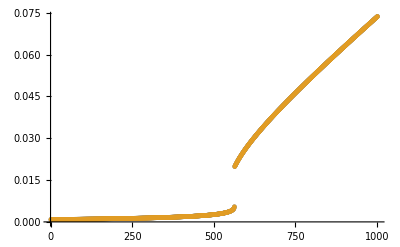

```mathematica
ListPlot[{ssx3i,Reverse[ssx3d]},PlotRange->Full]
```

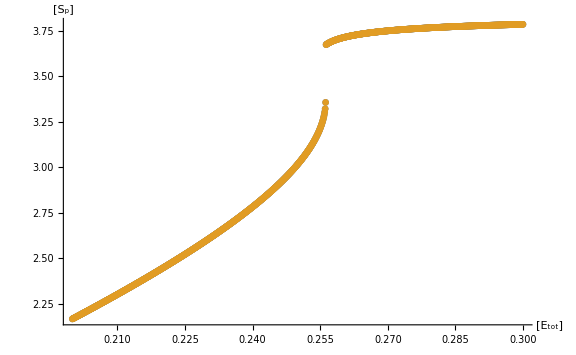

```mathematica
ListPlot[{Transpose@{Range[0.2,0.3,0.0001],ssx2i},Transpose@{Range[0.2,0.3,0.0001],Reverse[ssx2d]}},AxesLabel->{RawBoxes[RowBox[{"[",SubscriptBox["E","tot"],"]"}]],RawBoxes[RowBox[{"[",SubscriptBox["S","p"],"]"}]]},PlotLabel->None,LabelStyle->{16,GrayLevel[0]},ImageSize->Large,PlotRange->All]
```

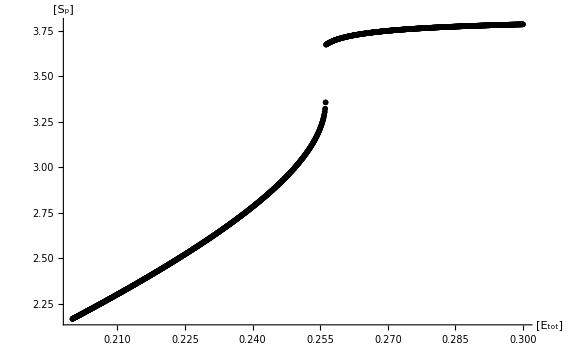

```mathematica
ListPlot[{Transpose@{Range[0.2,0.3,0.0001],ssx2i},Transpose@{Range[0.2,0.3,0.0001],Reverse[ssx2d]}},PlotTheme->"Monochrome",AxesLabel->{RawBoxes[RowBox[{"[",SubscriptBox["E","tot"],"]"}]],RawBoxes[RowBox[{"[",SubscriptBox["S","p"],"]"}]]},PlotLabel->None,LabelStyle->{16,GrayLevel[0]},ImageSize->Large,PlotRange->All]
```